This illustrates a GA (even multivector) parameterization of an ellipse.

```mathematica
<< GA30`;
```

```mathematica
ClearAll[e1,i,m,cosheven, ellipse]

e1 = Vector[1,1];
i = Bivector[1,1,2];
cosheven[m_grade, j_?bivectorQ] := Module[{s = m // ScalarValue, b  = -m . j // ScalarValue}, Cosh[s]Cos[b] + j Sinh[s]Sin[b]
]

ellipse[a_,b_, theta_] :=
Module[{alpha},
alpha=ArcTanh[b/a];
a e1 ** cosheven[Scalar[alpha] + theta *i ,i]/Cosh[alpha]
]

ellipse[3,2,θ]
```

3 Cos[θ] e_1+2 Sin[θ] e_2

The same parameterization can be used with complex numbers (which makes plotting easy)

```mathematica
ClearAll[ellipseComplex]

ellipseComplex[p_,a_,b_,rot_,theta_] := p + a Exp[I rot] Cosh[ArcTanh[b/a] + I theta]/Cosh[ArcTanh[b/a] ];

Manipulate[
Module[{el}, 
el = ellipseComplex[pr + I pi,a, a e,2 Pi r/360,#]&;
ParametricPlot[{el[t]//Re,el[t]//Im},{t,0,2Pi}]
],
{{pr,5, "x_0"}, 0, 100},
{{pi,5, "y_0"}, 0, 100},
{{a,5, "a"}, 1, 100},
{{e,0.5, "b/a"}, 0.001,1-0.001},
{{r,0,"θ"},0, 360/2}
]
```

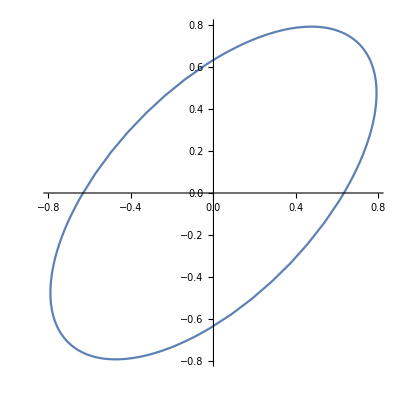

```mathematica
ellipseComplex2[p_,a_,b_,rot_,theta_] := p + a Exp[I rot] Cosh[ArcTanh[b/a] + I theta]Sqrt[1-(b/a)^2];

ClearAll[f]
f[a_,b_,al_, t_] := ellipseComplex[0,a,b,al,t]

With[{a=Pi/4},
ParametricPlot[ {f[1,0.5,a,t]// Re, f[1,0.5,a,t]// Im},{t,0,2 Pi}]]
```

```mathematica
ClearAll[a,b,es, t]
$Assumptions = a > 0 && b > 0 && a > b;
(*a Sqrt[1-(b/a)^2] Cosh[ ArcCosh[1/Sqrt[1-(b/a)^2]] + I t] // TrigExpand // FullSimplify*)
a Cosh[ ArcTanh[b/a] + I t]/Cosh[ ArcTanh[b/a] ]// TrigExpand // FullSimplify
a Sqrt[1-(b/a)^2]Cosh[ ArcTanh[b/a] + I t]// TrigExpand // FullSimplify
1/Cosh[ ArcTanh[b/a] ]// TrigExpand
a es Cosh[ ArcCosh[1/es] + I t]// TrigExpand // FullSimplify
```

a Cos[t]+ⅈ b Sin[t]

a Cos[t]+ⅈ b Sin[t]

√(1-b^2/a^2)

a (Cos[t]+ⅈ (1+es) √(-1+2/(1+es)) Sin[t])

```mathematica
x Sinh[ArcCosh[1/x]]
```

√((-1+1/x)/(1+1/x)) (1+1/x) x

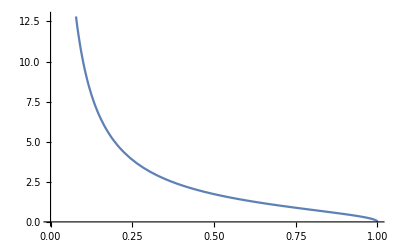

```mathematica
Plot[Sinh[ArcCosh[1/x]],{x,0,1}]
```